```mathematica
Msun=1476.7;
r0=10^6;
c=1;
μe=2;
me=9.109383*10^-31*7.4262*10^-28;
mH=1.672621923*10^-27*7.4262*10^-28;
h=1.6414*10^-69;
```

```mathematica
((3*h^3*ρ[x])/(8*Pi*μe*mH*(me*c)^3))^(1/3)
```

```mathematica
p[ρ[x_]]:=(Pi*me^4*c^5)/(3*h^3)*((((3*h^3*ρ[x])/(8*Pi*μe*mH*(me*c)^3))^(1/3))*(2*(((3*h^3*ρ[x])/(8*Pi*μe*mH*(me*c)^3))^(1/3))^2-3)*Sqrt[(((3*h^3*ρ[x])/(8*Pi*μe*mH*(me*c)^3))^(1/3))^2+1]+3*ArcSinh[((3*h^3*ρ[x])/(8*Pi*μe*mH*(me*c)^3))^(1/3)]);
```

13.5371

1.40968

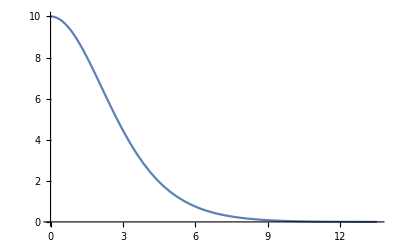
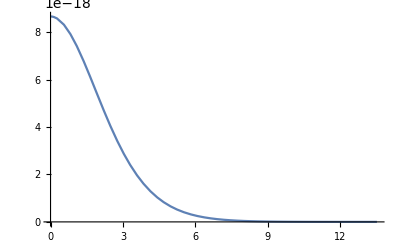
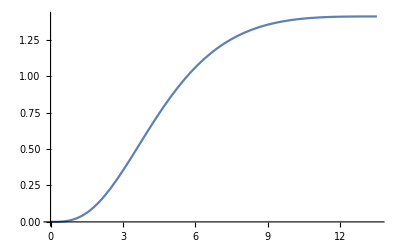

```mathematica
start=10^-20;
zerovalue=0;
sol=NDSolve[{(Msun*D[y[x],x])/r0==4*Pi*ρ[x]*(r0*x)^2+λ/2*(3*ρ[x]-p[ρ[x]])*(r0*x)^2,D[p[ρ[x]],x]/r0==-(p[ρ[x]]+ρ[x])*(4*Pi*p[ρ[x]]*(r0*x)+(Msun*y[x])/(r0*x)^2-(λ*(ρ[x]-3*p[ρ[x]])*(r0*x))/2)*(1-(2*Msun*y[x])/(r0*x))^(-1)*(1+λ/(8*Pi+2*λ)*(1-(D[ρ[x],x]/r0)/(D[p[ρ[x]],x]/r0)))^(-1),y[start]==zerovalue,ρ[start]==ρc}/.{λ->-10^-4,ρc->10^13*7.4262*10^-28},{y,ρ},{x,start,80}]//Quiet;
radius=x/.FindRoot[p[ρ[x]]/.sol,{x,1}]//Re//Quiet
mass=y[radius]/.sol[[1]]//Re//Quiet
{Plot[ρ[x]/(10^12*7.4262*10^-28)/.sol,{x,start,radius}],Plot[p[ρ[x]]/.sol,{x,start,radius}],Plot[y[x]/.sol,{x,start,radius}]}
```

{3.52853,3.20986,2.92141,2.63245}

{1.36481,1.36481,1.36481,1.36481}

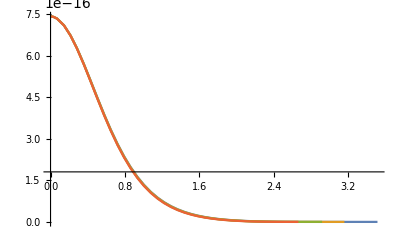

```mathematica
start=10^-15;
zerovalue=0;
soll=NDSolve[{(Msun*D[y[x],x])/r0==4*Pi*ρ[x]*(r0*x)^2+#/2*(3*ρ[x]-p[ρ[x]])*(r0*x)^2,D[p[ρ[x]],x]/r0==-(p[ρ[x]]+ρ[x])*(4*Pi*p[ρ[x]]*(r0*x)+(Msun*y[x])/(r0*x)^2-(#*(ρ[x]-3*p[ρ[x]])*(r0*x))/2)*(1-(2*Msun*y[x])/(r0*x))^(-1)*(1+#/(8*Pi+2*#)*(1-(D[ρ[x],x]/r0)/(D[p[ρ[x]],x]/r0)))^(-1),y[start]==0,ρ[start]==ρc}/.{ρc->10^12*7.4262*10^-28},{y,ρ},{x,start,5}]&/@Range[-4*10^-4,-1*10^-4,10^-4];
radius=x/.FindRoot[p[ρ[x]]/.#,{x,1}]&/@soll//Re//Quiet
mass=y[radius]/.sol[[1]]//Re//Quiet
Plot[{ρ[x]/.soll[[1]],ρ[x]/.soll[[2]],ρ[x]/.soll[[3]],ρ[x]/.soll[[4]]}(*{ρ[x]}/.soll[[All,1]]*),{x,start,Max[radius]},PlotRange->All](*Fug.3*)
```

## 开始循环

### For version

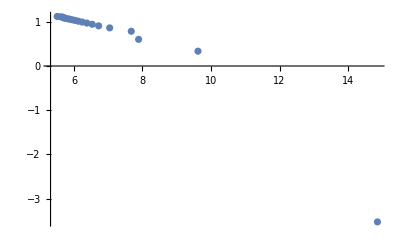

```mathematica
start=10^-20;
zerovalue=0;
lista={};
For[i=1,i<=100,i=i+5,cd=i*0.0005*10^12*7.4262*10^-28;sol=NDSolve[{(Msun*D[y[x],x])/r0==4*Pi*ρ[x]*(r0*x)^2+λ/2*(3*ρ[x]-p[ρ[x]])*(r0*x)^2,D[p[ρ[x]],x]/r0==-(p[ρ[x]]+ρ[x])*(4*Pi*p[ρ[x]]*(r0*x)+(Msun*y[x])/(r0*x)^2-(λ*(ρ[x]-3*p[ρ[x]])*(r0*x))/2)*(1-(2*Msun*y[x])/(r0*x))^(-1)*(1+λ/(8*Pi+2*λ)*(1-(D[ρ[x],x]/r0)/(D[p[ρ[x]],x]/r0)))^(-1),y[start]==zerovalue,ρ[start]==cd}/.{λ->-10^-4},{y,ρ},{x,start,5}];radius=x/.FindRoot[p[ρ[x]]/.sol[[1]],{x,1}]//Re;mass=y[radius]/.sol[[1]]//Re;lista=Append[lista,{radius,mass}]]//Parallelize//Quiet;
ListPlot[Thread[{lista[[All,1]],lista[[All,2]]}],PlotRange->All](*Fig.1*)
```

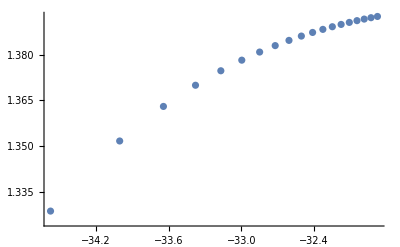

```mathematica
lista={};
For[i=1.3,i<=20,i=i+1,cd=i*10^12*7.4262*10^-28;sol=NDSolve[{(Msun*D[y[x],x])/r0==4*Pi*ρ[x]*(r0*x)^2+λ/2*(3*ρ[x]-p[ρ[x]])*(r0*x)^2,D[p[ρ[x]],x]/r0==-(p[ρ[x]]+ρ[x])*(4*Pi*p[ρ[x]]*(r0*x)+(Msun*y[x])/(r0*x)^2-(λ*(ρ[x]-3*p[ρ[x]])*(r0*x))/2)*(1-(2*Msun*y[x])/(r0*x))^(-1)*(1+λ/(8*Pi+2*λ)*(1-(D[ρ[x],x]/r0)/(D[p[ρ[x]],x]/r0)))^(-1),y[10^-15]==0,ρ[10^-15]==cd}/.{λ->10^-4},{y,ρ},{x,10^-15,5}];radius=x/.FindRoot[p[ρ[x]]/.sol[[1]],{x,1}]//Re;mass=y[radius]/.sol[[1]]//Re;lista=Append[lista,{Log[cd],mass}]]//Parallelize//Quiet;
ListPlot[Thread[{lista[[All,1]],lista[[All,2]]}],PlotRange->All](*Fig.4*)
```

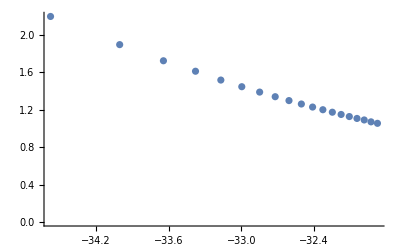

```mathematica
lista={};
For[Off[InterpolatingFunction::dmval];Off[FindRoot::lstol];i=1.3,i<=20,i=i+1,cd=i*10^12*7.4262*10^-28;sol=NDSolve[{(Msun*D[y[x],x])/r0==4*Pi*ρ[x]*(r0*x)^2+λ/2*(3*ρ[x]-p[ρ[x]])*(r0*x)^2,D[p[ρ[x]],x]/r0==-(p[ρ[x]]+ρ[x])*(4*Pi*p[ρ[x]]*(r0*x)+(Msun*y[x])/(r0*x)^2-(λ*(ρ[x]-3*p[ρ[x]])*(r0*x))/2)*(1-(2*Msun*y[x])/(r0*x))^(-1)*(1+λ/(8*Pi+2*λ)*(1-(D[ρ[x],x]/r0)/(D[p[ρ[x]],x]/r0)))^(-1),y[10^-15]==0,ρ[10^-15]==cd}/.{λ->10^-4},{y,ρ},{x,10^-15,5}];radius=x/.FindRoot[p[ρ[x]]/.sol[[1]],{x,1}]//Re;(*mass=y[radius]/.sol[[1]]//Re;*)lista=Append[lista,{Log[cd],radius}]]//Parallelize//Quiet;
ListPlot[Thread[{lista[[All,1]],lista[[All,2]]}],PlotRange->All](*Fig.5*)
```

### Do version

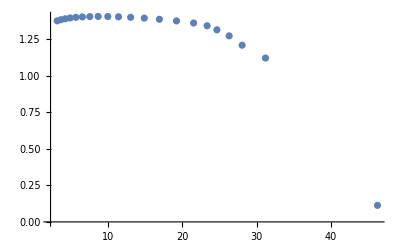
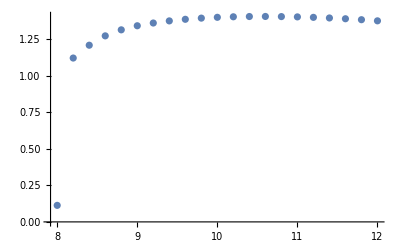
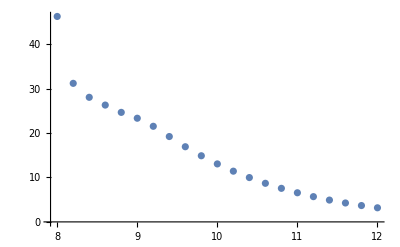

```mathematica
start=10^-5;
zerovalue=0;
list={};SetSharedVariable[list];
λ=0.;
ParallelDo[{sol=NDSolve[{(Msun*D[y[x],x])/r0==4*Pi*ρ[x]*(r0*x)^2+λ/2*(3*ρ[x]-p[ρ[x]])*(r0*x)^2,D[p[ρ[x]],x]/r0==-(p[ρ[x]]+ρ[x])*(4*Pi*p[ρ[x]]*(r0*x)+(Msun*y[x])/(r0*x)^2-(λ*(ρ[x]-3*p[ρ[x]])*(r0*x))/2)*(1-(2*Msun*y[x])/(r0*x))^(-1)*(1+λ/(8*Pi+2*λ)*(1-(D[ρ[x],x]/r0)/(D[p[ρ[x]],x]/r0)))^(-1),y[start]==zerovalue,ρ[start]==10^(i+3)*7.4262*10^-28}(*/.{λ->-4*10^-4,ρc->10^(i+3)*7.4262*10^-28}*),{y,ρ},{x,start,20}]//Quiet;
radius=x/.FindRoot[p[ρ[x]]/.sol,{x,1}]//Re//Quiet;
mass=y[radius]/.sol[[1]]//Re//Quiet;AppendTo[list,{radius,mass,i}]},{i,8.,12.,0.2}];
{ListPlot[Thread[{list[[All,1]],list[[All,2]]}],PlotRange->All(*{{0,20},{0,2}}*)](*Fig. 1*),ListPlot[Thread[{list[[All,3]],list[[All,2]]}],PlotRange->All(*{{8,11.5},{1.2,1.8}}*)](*Fig. 4*),ListPlot[Thread[{list[[All,3]],list[[All,1]]}],PlotRange->All(*{{8,11.5},{0,16}}*)](*Fig. 5*)}
```

## 我想算出来 λ = 0 的情况……

2.45351

1.34154

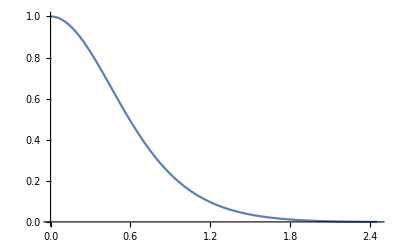
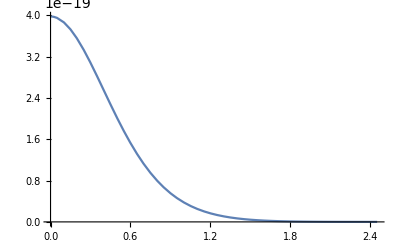
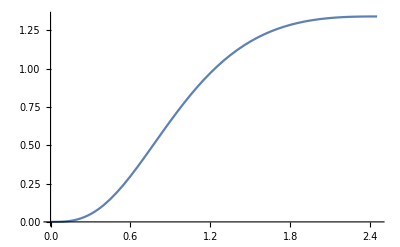

```mathematica
start=10^-5;
zerovalue=0;
ρc=10^12*7.4262*10^-28;
sol=NDSolve[{Msun/r0*D[y[x],x]==4*Pi*ρ[x]*(r0*x)^2,D[p[ρ[x]],x]/r0==-(p[ρ[x]]+ρ[x])*(4*Pi*p[ρ[x]]*(r0*x)+(Msun*y[x])/(r0*x)^2)*(1-(2*Msun*y[x])/(r0*x))^(-1),y[start]==zerovalue,ρ[start]==ρc},{y,ρ},{x,start,30}];
radius=x/.FindRoot[Re@p[ρ[x]]/.sol,{x,1}]
mass=Re@y[radius]/.First[sol]
{Plot[ρ[x]/ρc/.sol,{x,start,radius}],Plot[p[ρ[x]]/.sol,{x,start,radius}],Plot[y[x]/.sol,{x,start,radius}]}
```

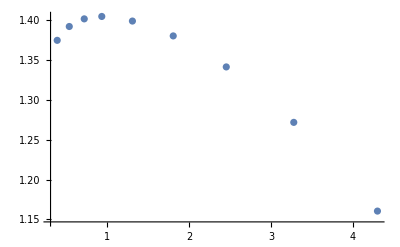
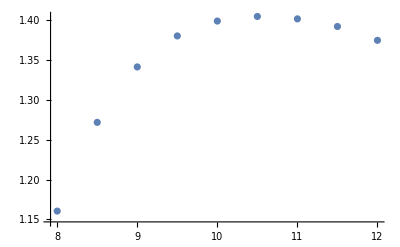
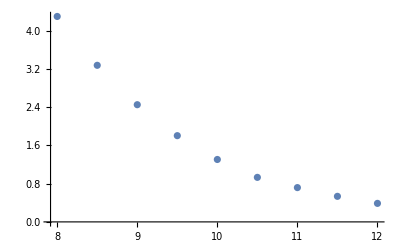

```mathematica
start=10^-5;
zerovalue=0;
list={};SetSharedVariable[list];
ParallelDo[{ρc=10^(i+3)*7.4262*10^-28;sol=NDSolve[{Msun/r0*D[y[x],x]==4*Pi*ρ[x]*(r0*x)^2,D[p[ρ[x]],x]/r0==-(p[ρ[x]]+ρ[x])*(4*Pi*p[ρ[x]]*(r0*x)+(Msun*y[x])/(r0*x)^2)*(1-(2*Msun*y[x])/(r0*x))^(-1),y[start]==zerovalue,ρ[start]==ρc},{y,ρ},{x,start,30}]//Quiet;radius=x/.FindRoot[Re@p[ρ[x]]/.sol,{x,1}]//Quiet;mass=Re@y[radius]/.First[sol]//Quiet;AppendTo[list,{i,radius,mass}]},{i,8.,12.,0.5}];
{ListPlot[Thread[{list[[All,2]],list[[All,3]]}],PlotRange->All(*{{0,20},{0,2}}*)](*Fig. 1*),ListPlot[Thread[{list[[All,1]],list[[All,3]]}],PlotRange->All(*{{8,11.5},{1.2,1.8}}*)](*Fig. 4*),ListPlot[Thread[{list[[All,1]],list[[All,2]]}],PlotRange->All(*{{8,11.5},{0,16}}*)](*Fig. 5*)}
```

## 我想还算出来 λ = - 2*10^-4 的情况……

6.7101287505878823738

1.25676

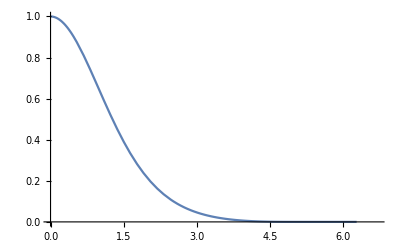
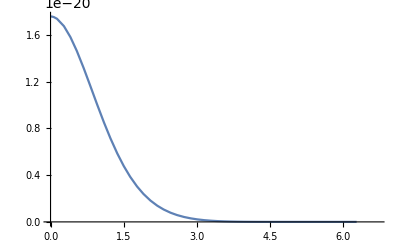
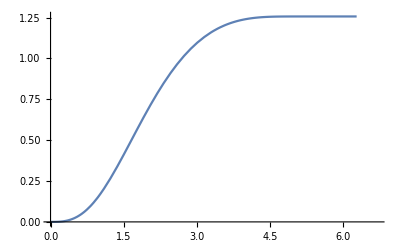

```mathematica
start=10^-20;
zerovalue=0;
λ=-2*10^-4;
ρc=10^11*7.4262*10^-28;
sol=NDSolve[{Msun/r0*D[y[x],x]==4*Pi*ρ[x]*(r0*x)^2+λ/2*(3*ρ[x]-p[ρ[x]])*(r0*x)^2,D[p[ρ[x]],x]/r0==-(p[ρ[x]]+ρ[x])*(4*Pi*p[ρ[x]]*(r0*x)+(Msun*y[x])/(r0*x)^2-(λ*(ρ[x]-p[ρ[x]])*(r0*x))/2)*(1-(2*Msun*y[x])/(r0*x))^(-1)*(1+λ/(8*Pi+2*λ)*(1-D[ρ[x],x]/D[p[ρ[x]],x]))^(-1),y[start]==zerovalue,ρ[start]==ρc},{y,ρ},{x,start,30}];
radius=x/.FindRoot[Re@p[ρ[x]]/.sol,{x,1},WorkingPrecision->20]//Quiet
mass=Re@y[radius]/.First[sol]
{Plot[ρ[x]/ρc/.sol,{x,start,radius}],Plot[p[ρ[x]]/.sol,{x,start,radius}],Plot[y[x]/.sol,{x,start,radius}]}
```

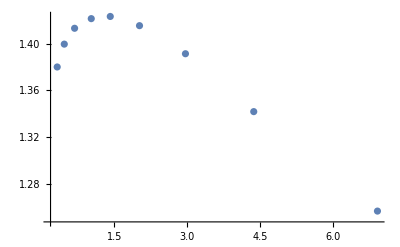
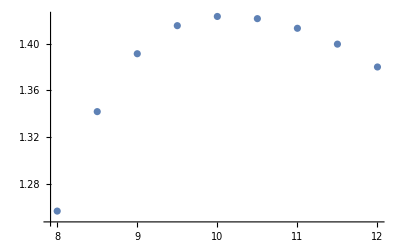
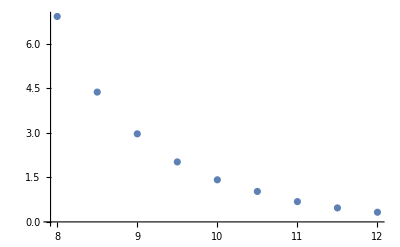

```mathematica
start=10^-5;
zerovalue=0;
λ=-2*10^-4;
list={};SetSharedVariable[list];
ParallelDo[{ρc=10^(i+3)*7.4262*10^-28;sol=NDSolve[{Msun/r0*D[y[x],x]==4*Pi*ρ[x]*(r0*x)^2+λ/2*(3*ρ[x]-p[ρ[x]])*(r0*x)^2,D[p[ρ[x]],x]/r0==-(p[ρ[x]]+ρ[x])*(4*Pi*p[ρ[x]]*(r0*x)+(Msun*y[x])/(r0*x)^2-(λ*(ρ[x]-p[ρ[x]])*(r0*x))/2)*(1-(2*Msun*y[x])/(r0*x))^(-1)*(1+λ/(8*Pi+2*λ)*(1-D[ρ[x],x]/D[p[ρ[x]],x]))^(-1),y[start]==zerovalue,ρ[start]==ρc},{y,ρ},{x,start,30}]//Quiet;radius=x/.FindRoot[Re@p[ρ[x]]/.sol,{x,1},WorkingPrecision->20]//Quiet;mass=Re@y[radius]/.First[sol]//Quiet;AppendTo[list,{i,radius,mass}]},{i,8.,12.,0.5}];
{ListPlot[Thread[{list[[All,2]],list[[All,3]]}],PlotRange->All(*{{0,20},{0,2}}*)](*Fig. 1*),ListPlot[Thread[{list[[All,1]],list[[All,3]]}],PlotRange->All(*{{8,11.5},{1.2,1.8}}*)](*Fig. 4*),ListPlot[Thread[{list[[All,1]],list[[All,2]]}],PlotRange->All(*{{8,11.5},{0,16}}*)](*Fig. 5*)}
```

## 我想还算出来 λ = - 4*10^-4 的情况……

1.41305521278049416051371493385

1.42336

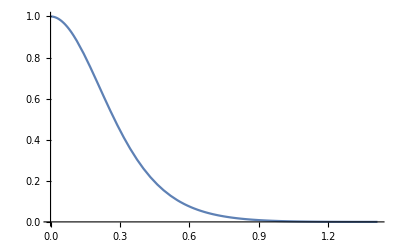
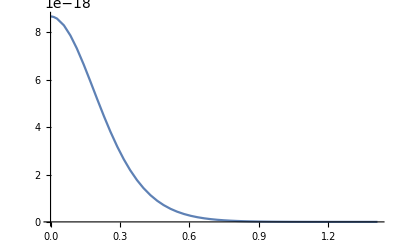
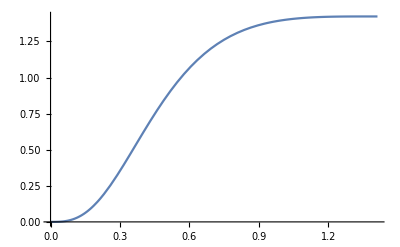

```mathematica
start=10^-20;
zerovalue=0;
λ=-2*10^-4;
ρc=10^(10+3)*7.4262*10^-28;
sol=NDSolve[{Msun/r0*D[y[x],x]==4*Pi*ρ[x]*(r0*x)^2+λ/2*(3*ρ[x]-p[ρ[x]])*(r0*x)^2,D[p[ρ[x]],x]/r0==-(p[ρ[x]]+ρ[x])*(4*Pi*p[ρ[x]]*(r0*x)+(Msun*y[x])/(r0*x)^2-(λ*(ρ[x]-p[ρ[x]])*(r0*x))/2)*(1-(2*Msun*y[x])/(r0*x))^(-1)*(1+λ/(8*Pi+2*λ)*(1-D[ρ[x],x]/D[p[ρ[x]],x]))^(-1),y[start]==zerovalue,ρ[start]==ρc},{y,ρ},{x,start,30}];
radius=x/.FindRoot[Re@p[ρ[x]]/.sol,{x,1},WorkingPrecision->30]//Quiet
mass=Re@y[radius]/.First[sol]
{Plot[ρ[x]/ρc/.sol,{x,start,radius}],Plot[p[ρ[x]]/.sol,{x,start,radius}],Plot[y[x]/.sol,{x,start,radius}]}
```

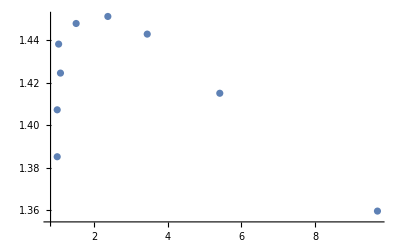
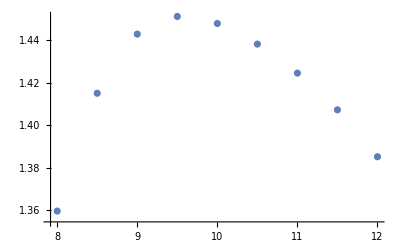
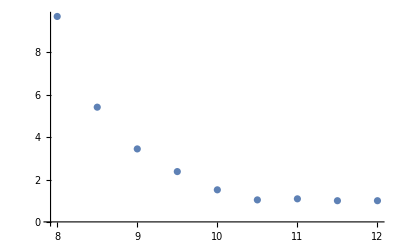

```mathematica
start=10^-5;
zerovalue=0;
λ=-4*10^-4;
list={};SetSharedVariable[list];
ParallelDo[{ρc=10^(i+3)*7.4262*10^-28;sol=NDSolve[{Msun/r0*D[y[x],x]==4*Pi*ρ[x]*(r0*x)^2+λ/2*(3*ρ[x]-p[ρ[x]])*(r0*x)^2,D[p[ρ[x]],x]/r0==-(p[ρ[x]]+ρ[x])*(4*Pi*p[ρ[x]]*(r0*x)+(Msun*y[x])/(r0*x)^2-(λ*(ρ[x]-p[ρ[x]])*(r0*x))/2)*(1-(2*Msun*y[x])/(r0*x))^(-1)*(1+λ/(8*Pi+2*λ)*(1-D[ρ[x],x]/D[p[ρ[x]],x]))^(-1),y[start]==zerovalue,ρ[start]==ρc},{y,ρ},{x,start,30}]//Quiet;radius=x/.FindRoot[Re@p[ρ[x]]/.sol,{x,1},WorkingPrecision->10]//Quiet;mass=Re@y[radius]/.First[sol]//Quiet;AppendTo[list,{i,radius,mass}]},{i,8.,12.,0.5}];
{ListPlot[Thread[{list[[All,2]],list[[All,3]]}],PlotRange->All(*{{0,20},{0,2}}*)](*Fig. 1*),ListPlot[Thread[{list[[All,1]],list[[All,3]]}],PlotRange->All(*{{8,11.5},{1.2,1.8}}*)](*Fig. 4*),ListPlot[Thread[{list[[All,1]],list[[All,2]]}],PlotRange->All(*{{8,11.5},{0,16}}*)](*Fig. 5*)}
```

```mathematica
Quit[]
```